```mathematica
coordinatesPath = "/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/ConvexHull/Helpers/Text files/coordinates.txt";
firstMethodPath = "/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/ConvexHull/Helpers/Text files/ConvexHullPoints(MethodII).txt";
secondMethodPath = "/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/ConvexHull/Helpers/Text files/ConvexHullPoints(MethodI).txt";

numberOfPoints = ToExpression[
Import[coordinatesPath, {"Lines", 1} ]
];
```

```mathematica
points = {};
For[i = 2, i < numberOfPoints* 2 + 2, i+= 2, 
AppendTo[points,Point[ToExpression[
Take[
Import[coordinatesPath,"Words"],{i, i+1}]
]
]
]
]
```

```mathematica
numberOfConvexHullPoints = ToExpression[Import[firstMethodPath, {"Lines", 1}]];
convexHullPoints = {};
For[i = 2, i < numberOfConvexHullPoints * 2 + 2, i+= 2, AppendTo[convexHullPoints,ToExpression[Take[Import[firstMethodPath, "Words"],{i, i+1}]]]
]
AppendTo[convexHullPoints, Part[convexHullPoints, 1]]
```

{{-9554.09,-1481.52},{-7011.91,7621.98},{-6327.39,8246.97},{6867.73,9304.36},{8907.37,8420.4},{9825.5,7533.56},{-9554.09,-1481.52},{-8415.11,-4153.95},{-4103.13,-8856.48},{4885.15,-9610.95},{9346.93,-5194.16},{9825.5,7533.56},{-9554.09,-1481.52}}

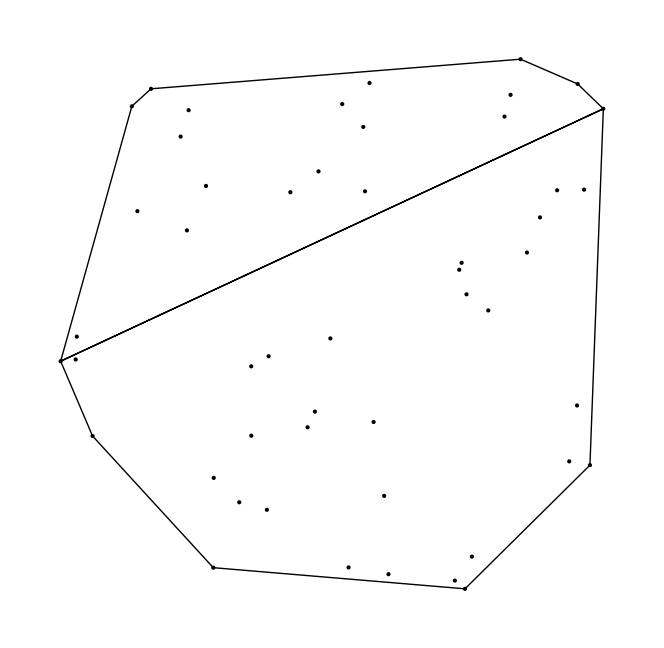

```mathematica
Graphics[{points,Line[convexHullPoints]}]
```